```mathematica
Clear["Global`*"]

(*---Matter-dominated perturbation equation---*)
n=-2/3;
δ=f[x]*x^n;
δDot=D[δ,x]*k;
δDotDot=D[δDot,x]*k;
perturbationEqn=δDotDot+4/(3 t) δDot==2/(3 t^2) (1-(cs^2 k^2)/(4 π G Subscript[ρ,0] a^2)) δ/. t->x/k/. Subscript[ρ,0]->(3 H0^2)/(8 π G a^3);
FofX=DSolve[perturbationEqn,f[x],x][[1,1,2]];
δofX=FullSimplify[FofX*x^n];
δofKA=δofX/. x->((2 k a^(3/2))/(3 H0));

(*---Hubble parameter and gravitational potential---*)
H[a_]:=H0 Sqrt[Ωm/a^3];
Ψ[a_]:=-(3 H0^2 Ωm)/(2 a^3);

(*---Solve perturbation equation---*)
ceff2[a_]:=0;
negligibleSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
ceff2[a_]:=cs^2;
perturbedSolution=DSolve[a^2 H[a]^2 Δa''[a]+(3 a H[a]^2+a^2 H[a] H'[a]) Δa'[a]+(k^2 ceff2[a]^2/a^2+Ψ[a]) Δa[a]==0,Δa,a]//FullSimplify;
negligibleFunc=negligibleSolution[[1,1,2]];
perturbedFunc=Function[{a},(3/2)^((H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) ((a^(3/2) k)/H0)^(-((H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0))) C[1]+(2/3)^(Sqrt[25 H0^2-16 a cs^2 k^2]/(3 H0)-(H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) ((a^(3/2) k)/H0)^(Sqrt[25 H0^2-16 a cs^2 k^2]/(3 H0)-(H0+Sqrt[25 H0^2-16 a cs^2 k^2])/(6 H0)) C[2]];

(*---Matching functions and derivatives at the start and end of the "kick"---*)
solutionsForConstants1=Solve[{ai CC==perturbedFunc[ai],CC==D[perturbedFunc[a],a]/. a->ai},{C[1],C[2]}]//FullSimplify;
startKick=perturbedFunc/. {C[1]->solutionsForConstants1[[1,1,2]],C[2]->solutionsForConstants1[[1,2,2]]};
solutionsForConstants2=Solve[{(negligibleFunc[af])==(startKick[af]),(D[negligibleFunc[a],a]/. a->af)==(D[startKick[a],a]/. a->af)},{C[1],C[2]}]//Simplify;
endKick=negligibleFunc/. {C[1]->solutionsForConstants2[[1,1,2]],C[2]->solutionsForConstants2[[1,2,2]]};

(*---Piecewise perturbation solution---*)
δgdm[a_]:=Piecewise[{{CC a,a<ai},{startKick[a],ai<=a<=af}},endKick[a]];

(*---Gravitational potential via the Poisson equation substitution---*)
phi[a_]:=-(3/2)*a*H[a]^2/k^2*δgdm[a];
phiExpr=Simplify[phi[a],Assumptions->{a>0,k>0,H0>0,Ωm>0}];
(*phiExpr // TraditionalForm*)
(*Runtime: ~49 secs*)
```

```mathematica
(*---Plotting δ, we compare against Tristan---*)
(*GraphicsRow[{
LogLinearPlot[(Abs[CC a-δgdm[a]])/(CC a),{a,0.0001*ai,1},PlotRange->All,PlotLabel->"Fractional Difference"],LogLinearPlot[(-δgdm[a]*Ψ[a]*a^2+CC*a*Ψ[a]*a^2)/k^2,{a,0.0001*ai,1}],
Plot[(lg[Exp[x+0.01]]-lg[Exp[x-0.01]])/0.02,{x,Log[ai]-0.001,Log[af]+0.001}]}
]*)
```

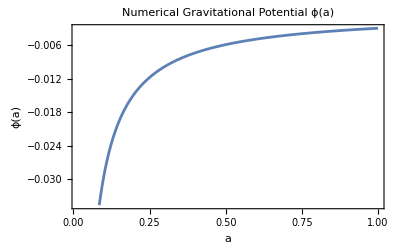

```mathematica
(*---Numerics---*)
h=0.7;
H0=0.0003335*h;
Ωm=1;
k=0.00528;
ai=0.01489;
af=0.02;
cs2want=0.0001;
da=Log[af/ai];
cs=Sqrt[cs2want/da];
CC=1;

(*---Numerical versions of the analytic functions---*)
deltaGDMNum[a_]:=δgdm[a]/. {H0->H0,Ωm->Ωm,k->k,ai->ai,af->af,cs->cs,CC->CC};
phiNum[a_]:=phi[a]/. {H0->H0,Ωm->Ωm,k->k,ai->ai,af->af,cs->cs,CC->CC};

(*---Plot the numerical gravitational potential---*)
Plot[phiNum[a],{a,ai,1},PlotLabel->"Numerical Gravitational Potential ϕ(a)",Frame->True,AxesLabel->{"a","ϕ(a)"}]
```

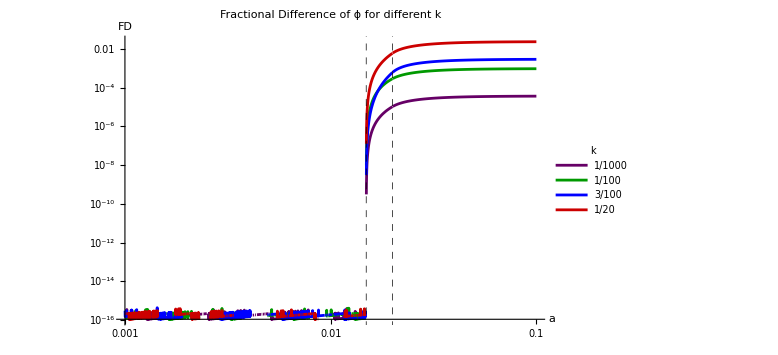

```mathematica
(*---Plot the fractional difference of gravitational potential---*)
phiRef[kVal_?NumericQ,a_]:=-(3/2)*a*H[a]^2/(kVal^2)*(CC*a); (**)
FDphi[kVal_?NumericQ,a_]:=Abs[(phiRef[kVal,a]-(phi[a]/. {k->kVal}))/phiRef[kVal,a]]; (**)
kVals={10^-3,10^-2,3*10^-2,5*10^-2};
colors={RGBColor[0.4,0,0.4],RGBColor[0,0.6,0],Blue,RGBColor[0.8,0,0]};
LogLogPlot[
Evaluate[Table[FDphi[k,a],{k,kVals}]],{a,0.0010,0.1},
PlotRange->All,
PlotStyle->colors,
AxesLabel->{"a","FD"},
PlotLegends->Placed[LineLegend[kVals,LegendLabel->"k"],{Right,Bottom}],
GridLines->{{ai,af},None},
GridLinesStyle->Directive[Black,Dashed,Thick],
PlotLabel->"Fractional Difference of ϕ for different k",
ImageSize->Large
]
```

```mathematica
ai=0.01489;
af=0.02;
kVals={10^-3,10^-2,3*10^-2,5*10^-2};

(*Create data in log space, taking 50 steps from ai to af*)
makeData[k_?NumericQ]:=Module[{n=50,logAi=Log[ai],logAf=Log[af],dt,aval},dt=(logAf-logAi)/n;
Table[(aval=Exp[logAi+i*dt];
{Log[aval],Log[FDphi[k,aval]]}),{i,0,n}]];

(*Filter out bad points and do linear fit. Slope in ln-ln space is power-law exponent.*)
slopeFit[k_?NumericQ]:=Module[{rawData,goodData,lm},rawData=makeData[k];
goodData=Select[rawData,FreeQ[#,Indeterminate]&&FreeQ[#,Infinity]&&NumericQ[#[[1]]]&&NumericQ[#[[2]]]&];
lm=LinearModelFit[goodData,x,x];
lm["BestFitParameters"][[2]]];

(*Evaluate slopes for each k in kVals*)
slopes=slopeFit/@kVals
```

{-0.0000179773,0.000669926,0.000498616,0.000488621}

```mathematica
(*Dense grid, smaller timestep, find analytic scaling *)
(*Put in specific numeric values, and try finding a clean way to see Subscript[c, 1,2] wrt a*)
(*Try a slower kick*)
```

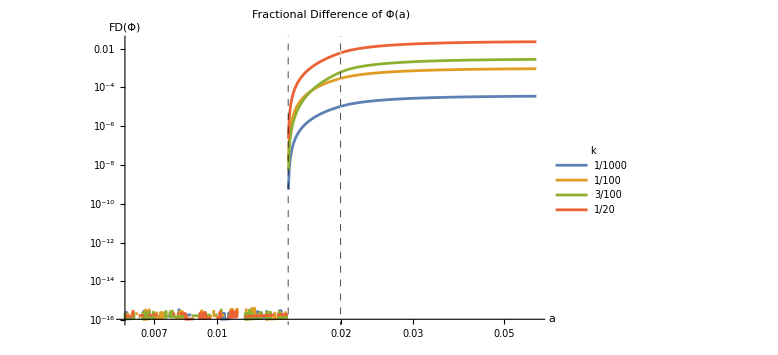

```mathematica
ai=0.01489;
af=0.02;   
h=0.7;
H0=0.0003335*h;
Ωm=1;
cs2want=0.0001;
da=Log[af/ai];
cs=Sqrt[cs2want/da];
CC=1; (*We don't always want to normalize the kick, and we don't always have clean ICs*)

δgdm[a_]:=Piecewise[{{CC*a,a<ai},{startKick[a],ai<=a<=af}},endKick[a]];
phi[a_]:=-(3/2)*a*H[a]^2/(k^2)*(δgdm[a]);
phiRef[k_?NumericQ,a_]:=-(3/2)*a*H[a]^2/(k^2)*(CC*a);
FDphi[k_?NumericQ,a_]:=Abs[(phiRef[k,a]-(phi[a]/. {k->k}))/phiRef[k,a]];

kVals={10^-3,10^-2,3*10^-2,5*10^-2};
colors={RGBColor[0.4,0,0.4],RGBColor[0,0.6,0],Blue,RGBColor[0.8,0,0]};

LogLogPlot[
Evaluate[Table[FDphi[k,a],{k,kVals}]],{a,0.4*ai,3*af},
PlotRange->All,
PlotPoints->150,
MaxRecursion->3,
AxesLabel->{"a","FD(Φ)"},
PlotLegends->Placed[LineLegend[kVals,LegendLabel->"k"],{Right,Bottom}],
GridLines->{{ai,af},None},
GridLinesStyle->Directive[Black,Dashed,Thick],
PlotLabel->"Fractional Difference of Φ(a)",
ImageSize->Large
]
```

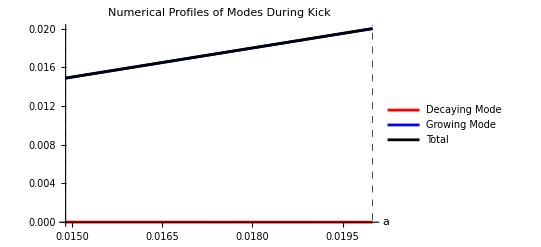

```mathematica
(*Same constants as above*)
ai=0.01489;
af=0.020;   
h=0.7;
H0=0.0003335*h;
Ωm=1;
cs2want=0.0001;
da=Log[af/ai];
cs=Sqrt[cs2want/da];
CC=1;
k0=0.00528; (*Differentiate from k (analytic)*)
(*k0=0.00528*)

(*Borrow the two modes from full analytic solution*)
decayingMode[a_]:=(3/2)^((H0+√(25 H0^2-16 a cs^2 k^2))/(6 H0)) ((a^(3/2) k)/H0)^(-(H0+√(25 H0^2-16 a cs^2 k^2))/(6 H0)) C[1];
growingMode[a_]:=(2/3)^((√(25 H0^2-16 a cs^2 k^2))/(3 H0)-(H0+√(25 H0^2-16 a cs^2 k^2))/(6 H0)) ((a^(3/2) k)/H0)^((√(25 H0^2-16 a cs^2 k^2))/(3 H0)-(H0+√(25 H0^2-16 a cs^2 k^2))/(6 H0)) C[2];

(*Substitute the constants determined at the start of the kick*)
decayingModeStart[a_]:=decayingMode[a]/. {C[1]->solutionsForConstants1[[1,1,2]]};
growingModeStart[a_]:=growingMode[a]/. {C[2]->solutionsForConstants1[[1,2,2]]};

(*Define the numerical versions as functions of a,fixing k=k0*)
decayingModeNumerical[a_]:=Evaluate[decayingModeStart[a]/. {k->k0}];
growingModeNumerical[a_]:=Evaluate[growingModeStart[a]/. {k->k0}];

(*Plot the absolute values of each mode and their sum over the interval from 0.4*ai to 3*af*)
Plot[
{decayingModeNumerical[a],growingModeNumerical[a],decayingModeNumerical[a]+growingModeNumerical[a]},{a,ai,af},
PlotLegends->{"Decaying Mode","Growing Mode","Total"},
AxesLabel->{"a"},
PlotRange->All,
PlotPoints->150,
MaxRecursion->3,
GridLines->{{ai,af},None},
GridLinesStyle->Directive[Black,Dashed,Thick],
PlotLabel->"Numerical Profiles of Modes During Kick",
PlotStyle->{Red,Blue,{Black}}
]
(*k on order 1/Subscript[c, s] to expect oscillations*)
(*Check absolute thing*)
(*Add more k values*)
```